```mathematica
sp500 = Transpose[Import["C:\\Users\\Eakka\\Desktop\\New folder\\intra D log return.csv"]];
sp500 = sp500[[1]];
FindDistributionParameters[sp500,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[sp500,NormalDistribution[μ, σ]]
```

{μ→4.06993×10^-7,β→0.000115804,q→1.7037}

{μ→4.06993×10^-7,σ→0.000351343}

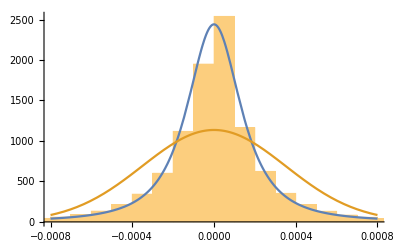

```mathematica
Show[Histogram[sp500,Automatic,"ProbabilityDensity"],Plot[{PDF[TsallisQGaussianDistribution[0,0.00011580,1.70],x],PDF[NormalDistribution[0,0.00035134],x]},{x,-0.0008,0.0008}]]
```

```mathematica
s1 = sp500[[1000;;2000]];
FindDistributionParameters[s1,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[s1,NormalDistribution[μ, σ]]
```

{μ→-3.01368×10^-6,β→0.000281734,q→1.51983}

{μ→-3.01368×10^-6,σ→0.000524434}